#### Contains functions defined in “Q-balls stopping power” file

```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Charged Pion-Carbon scattering

```mathematica
Emaxfull:=(2M*β^2*γ^2)/(1+2γ*(M/mπ)+(M/mπ)^2)
```

```mathematica
Equantum=(2 mπ^2 Z^2 α^2 γ^2)/M;
```

```mathematica
ebound[b_]:=2Z^2*α^2/(M*b^2*β^2)
```

```mathematica
ebound[1/me]//FullSimplify
```

(2 me^2 Z^2 α^2)/(M β^2)

```mathematica
ebound[1/(mπ*β*γ)]//FullSimplify
```

(2 mπ^2 Z^2 α^2 γ^2)/M

```mathematica
Emaxfullmax:=Min[Emaxfull,Equantum,M]
```

```mathematica
dσdE/.me->M
```

(2 π Z^2 α^2 (1-(Ed β^2)/emax))/(Ed^2 M β^2)

```mathematica
Integrate[n(2 π Z^2 α^2)/(Ed^2 M β^2)*Ed,Ed]
```

(2 n π Z^2 α^2 Log[Ed])/(M β^2)

#### Mass of carbon nuclei (from Wolfram Alpha)

```mathematica
Convert[1.993*10^-23 Gram*SpeedOfLight^2,Mega ElectronVolt]
```

11179.9 ElectronVolt Mega

```mathematica
dEdxcarbon=Pi*(n*Z^2*α^2)/(M*β^2)Log[(Emaxfull/((2 me^2 Z^2 α^2)/(M β^2)))^2+1]/.{γ->1/Sqrt[1-β^2]}/.{β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)};
```

```mathematica
dEdxcarbonmax=Pi*(n*Z^2*α^2)/(M*β^2)Log[(Emaxfullmax/((2 me^2 Z^2 α^2)/(M β^2)))^2+1]/.{γ->1/Sqrt[1-β^2]}/.{β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)};
```

#### Use the screening length ~ 1/MeVto set minimum energy transfer. Maximum energy transfer is due to kinematics

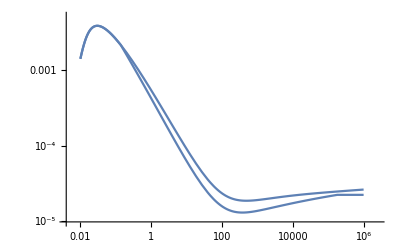

```mathematica
LogLogPlot[{dEdxcarbon,dEdxcarbonmax}/.{n->0.8,me->0.511,M->11180,α->1/137,mπ->139.57,Z->6},{Eπ,10^-2,10^6}]
```

#### Soft scattering is imbedded into this formalism. Turning point occurs when β drops below 1, Eπ<mπ.

```mathematica
Table[Convert[(NIntegrate[dEdxcarbonmax^-1/.{me->0.511,n->0.8,M->11180,α->1/137,mπ->140,Z->6},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{500,10^3,10^4,10^5,10^6}}]
```

{0.000389139 Centimeter,0.000759067 Centimeter,0.00604365 Centimeter,0.0488208 Centimeter,0.453861 Centimeter}

```mathematica
Table[Convert[(NIntegrate[dedxpauli^-1/.{M->0.511,me->0.511,α->1/137,mπ->139.57,Z->1,n->8},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{500,10^3,10^4,10^5,10^6}}]
```

{0.0057049 Centimeter,0.00386774 Centimeter,0.000544561 Centimeter,0.00158354 Centimeter,0.0158355 Centimeter}

#### Total:

```mathematica
dEdxcarbonpion=dEdxcarbonmax/.{n->0.8,me->0.511,M->11180,α->1/137,mπ->139.57,Z->6};
```

```mathematica
dEdxelectronpion=dedxpauli/.{n->8,me->0.511,M->0.511,α->1/137,mπ->139.57,Z->1};
```

```mathematica
Table[Convert[(NIntegrate[(dEdxcarbonpion+dEdxelectronpion)^-1,{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{500,10^3,10^4,10^5,10^6}}]
```

{0.000362559 Centimeter,0.000625711 Centimeter,0.000494328 Centimeter,0.00153378 Centimeter,0.0153017 Centimeter}

#### For those pesky muons, SP is approximately the same.

```mathematica
Table[Convert[(NIntegrate[dEdxcarbonmax^-1/.{me->0.511,n->0.8,M->11180,α->1/137,mπ->100,Z->6},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{500,10^3,10^4,10^5,10^6}}]
```

{0.000406197 Centimeter,0.000772595 Centimeter,0.00604817 Centimeter,0.0488232 Centimeter,0.453861 Centimeter}

```mathematica
Table[Convert[(NIntegrate[dedxpauli^-1/.{M->0.511,me->0.511,α->1/137,mπ->100,Z->1,n->8},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{500,10^3,10^4,10^5,10^6}}]
```

{0.00345343 Centimeter,0.00219122 Centimeter,0.000285409 Centimeter,0.00158355 Centimeter,0.0158355 Centimeter}

#### Total

```mathematica
dEdxcarbonmuon=dEdxcarbonmax/.{n->0.8,me->0.511,M->11180,α->1/137,mπ->100,Z->6};
```

```mathematica
dEdxelectronmuon=dedxpauli/.{n->8,me->0.511,M->0.511,α->1/137,mπ->100,Z->1};
```

```mathematica
Table[Convert[(NIntegrate[(dEdxcarbonmuon+dEdxelectronmuon)^-1,{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{500,10^3,10^4,10^5,10^6}}]
```

{0.000360249 Centimeter,0.000559226 Centimeter,0.00027095 Centimeter,0.00153379 Centimeter,0.0153017 Centimeter}

#### And what about electrons?

```mathematica
Table[Convert[(NIntegrate[dEdxcarbonmax^-1/.{me->0.511,n->0.8,M->11180,α->1/137,mπ->0.5,Z->6},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{500,10^3,10^4,10^5,10^6}}]
```

{0.000440944 Centimeter,0.000797794 Centimeter,0.00605802 Centimeter,0.048829 Centimeter,0.453861 Centimeter}

```mathematica
Table[Convert[(NIntegrate[dedxpauli^-1/.{M->0.511,me->0.511,α->1/137,mπ->0.511,Z->1,n->8},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{500,10^3,10^4,10^5,10^6}}]
```

{7.91774×10^-6 Centimeter,0.0000158355 Centimeter,0.000158355 Centimeter,0.00158355 Centimeter,0.0158355 Centimeter}

#### How about the totals?

```mathematica
dEdxcarbonelectron=dEdxcarbonmax/.{n->0.8,me->0.511,M->11180,α->1/137,mπ->0.511,Z->6};
```

```mathematica
dEdxelectronelectron=dedxpauli/.{n->8,me->0.511,M->0.511,α->1/137,mπ->0.511,Z->1};
```

```mathematica
Table[Convert[(NIntegrate[(dEdxcarbonelectron+dEdxelectronelectron)^-1,{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{500,10^3,10^4,10^5,10^6}}]
```

{7.77795×10^-6 Centimeter,0.0000155271 Centimeter,0.00015432 Centimeter,0.0015338 Centimeter,0.0153017 Centimeter}

#### What about an ~MeV charged particle, say a proton?

```mathematica
Table[Convert[(NIntegrate[dEdxcarbonmax^-1/.{me->0.511,n->0.8,M->11180,α->1/137,mπ->1000,Z->6},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{1,10}}]
```

{2.10407×10^-9 Centimeter,1.56625×10^-7 Centimeter}

#### At low energies, you need the ions to come save you.